This file is for Physical Informatics II 2016/04/15
Authored by Haochen Xie

# Question 2

```mathematica
qx[t_]:=16240/(2056-t)^(7/5)
```

```mathematica
diff=D[qx[t],t]-(r qx[t]^(5/7)) qx[t]
```

-64960 2^(6/7) 1015^(5/7) r (1/(2056-t)^(7/5))^(12/7)+22736/(2056-t)^(12/5)

```mathematica
Solve[diff==0]//N
```

{{r→0.00085782+0.00107567 ⅈ},{r→0.00137584},{r→-0.00123959-0.000596953 ⅈ},{r→-0.000306152-0.00134134 ⅈ},{r→-0.000306152+0.00134134 ⅈ},{r→0.00085782-0.00107567 ⅈ},{r→-0.00123959+0.000596953 ⅈ}}

Thus D[x[t],t]==(r x[t]^(5/7))x[t] when r→0.00137584

```mathematica
Sraw=DSolve[D[x[t],t]==(r x[t]^(5/7))x[t],x,t]
S=Simplify[Sraw⟦1,1,2,2⟧]
```

{{x→Function[{t},-(7 (7/5)^(2/5))/(5 (-r t-C[1])^(2/5) (r t+C[1]))]}}

(7 (7/5)^(2/5))/(5 (-r t-C[1])^(7/5))

We can transform S to (7 (7/5)^(2/5))/(5 r^(7/5)(C[2]-t)^(7/5))

```mathematica
Solve[(7 (7/5)^(2/5))/(5 r^(7/5)(C[2]-t)^(7/5))==qx[t]/.C[2]->2056]
```

{{r→7^(2/7)/(20 2^(6/7) 145^(5/7))}}

That is, qx is an instance of S.

Question 3

```mathematica
Fdeq:=D[x[t],t]==r x[t](1-x[t]/K)
```

```mathematica
Fsolraw=DSolve[Fdeq,x,t]
Fsol=Fsolraw⟦1,1,2,2⟧
```

{{x→Function[{t},(ⅇ^(r t+K C[1]) K)/(-1+ⅇ^(r t+K C[1]))]}}

(ⅇ^(r t+K C[1]) K)/(-1+ⅇ^(r t+K C[1]))

```mathematica
Fsolraw2=DSolve[{Fdeq,x[0]==x0},x,t]//Simplify
Fsol2=Fsolraw2⟦1,1,2,2⟧
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Function[{t},(ⅇ^(r t) K x0)/(K-x0+ⅇ^(r t) x0)]}}

(ⅇ^(r t) K x0)/(K-x0+ⅇ^(r t) x0)

```mathematica
Reduce[Fsol2==(K x0 ⅇ^(r t))/(K + x0 (ⅇ^(r t)-1))]
```

True

Question 4

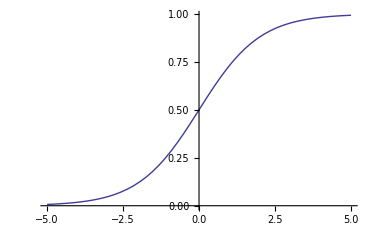

```mathematica
Plot[1/(1+ⅇ^(-1x)),{x,-5,5}]
```